# Brezposelnost v državah OECD

## Pridobivanje podatkov

Podatke v CSV formatu pridobimo s spletne strani OECD.

```mathematica
podatki=Import["C:\\Users\\katis\\ROM-projekt2\\podatki_OECD.csv","Dataset",HeaderLines->1]
```

Dataset[<>]

V prvem stolpcu je ime držav, za katere imamo podatke:

```mathematica
podatki[All,1]//DeleteDuplicates
```

Dataset[<>]

Te kratice moramo povezati z dejanskimi državami članicami OECD.

```mathematica
EntityList[EntityClass["Country","OrganizationForEconomicCooperationAndDevelopment"]]
```

{Australia,Austria,Belgium,Canada,Chile,Czech Republic,Denmark,Estonia,Finland,France,Germany,Greece,Hungary,Iceland,Ireland,Israel,Italy,Japan,Luxembourg,Mexico,Netherlands,New Zealand,Norway,Poland,Portugal,Slovakia,Slovenia,South Korea,Spain,Sweden,Switzerland,Turkey,United Kingdom,United States}

Naslednji slovar vnesemo ročno. Nekaj članic v zgornjem seznamu manjka (države so izstopile iz OECD ali pa pred kratkim vstopile). Te države dodamo ročno. Sestavimo še obratni slovar.

```mathematica
slovarDrzav=<|Entity["Country","Australia"]->"AUS",Entity["Country","Austria"]->"AUT",Entity["Country","Belgium"]->"BEL",Entity["Country","Canada"]->"CAN",Entity["Country","Chile"]->"CHL",Entity["Country","CzechRepublic"]->"CZE",Entity["Country","Denmark"]->"DNK",Entity["Country","Estonia"]->"EST",Entity["Country","Finland"]->"FIN",Entity["Country","France"]->"FRA",Entity["Country","Germany"]->"DEU",Entity["Country","Greece"]->"GRC",Entity["Country","Hungary"]->"HUN",Entity["Country","Iceland"]->"ISL",Entity["Country","Ireland"]->"IRL",Entity["Country","Israel"]->"ISR",Entity["Country","Italy"]->"ITA",Entity["Country","Japan"]->"JPN",Entity["Country","Luxembourg"]->"LUX",Entity["Country","Mexico"]->"MEX",Entity["Country","Netherlands"]->"NLD",Entity["Country","NewZealand"]->"NZL",Entity["Country","Norway"]->"NOR",Entity["Country","Poland"]->"POL",Entity["Country","Portugal"]->"PRT",Entity["Country","Slovakia"]->"SVK",Entity["Country","Slovenia"]->"SVN",Entity["Country","SouthKorea"]->"KOR",Entity["Country","Spain"]->"ESP",Entity["Country","Sweden"]->"SWE",Entity["Country","Switzerland"]->"CHE",Entity["Country","Turkey"]->"TUR",Entity["Country","UnitedKingdom"]->"GBR",Entity["Country","UnitedStates"]->"USA",Entity["Country","Latvia"]->"LVA",Entity["Country","Lithuania"]->"LTU",Entity["Country","Colombia"]->"COL"|>;
slovarKratic=AssociationList[Reverse,slovarDrzav];
```

V stolpcu “FREQUENCY” imamo tip podatka (letni/četrtletni/mesečni):

```mathematica
podatki[All,"FREQUENCY"]//DeleteDuplicates
```

Dataset[<>]

## Časovni pregled brezposelnosti v posameznih državah

Ker bomo podatke analizirali za vse države, bomo definirali funkcijo, ki kot argument vzame državo in vrne podatke o letu in stopnji brezposelnosti. Pri tem vzamemo le celoletne podatke. Če kot argument podamo spol, funkcija vrne le izbrane podatke.

```mathematica
Clear[podatkiZaDrzavo]
podatkiZaDrzavo[drzava_]:=podatki[Select[#"\"LOCATION\""==slovarDrzav[drzava]&&#FREQUENCY=="A"&],{"SUBJECT","TIME","Value"}]
podatkiZaDrzavo[drzava_,spol_]:=podatki[Select[#"\"LOCATION\""==slovarDrzav[drzava]&&#FREQUENCY=="A"&&#"SUBJECT"==spol&],{"TIME","Value"}]
```

```mathematica
podatkiZaDrzavo[Entity["Country","Slovenia"]]
```

Dataset[<>]

```mathematica
podatkiZaDrzavo[Entity["Country","Slovenia"],"WOMEN"]
```

Dataset[<>]

Naslednja funkcija za seznam držav izriše njihove podatke (le za subject = “TOT” - oba spola).

```mathematica
Clear[Narisi]
Narisi[seznamdrzav__]:=ListLinePlot[podatkiZaDrzavo[#,"TOT"]&/@{seznamdrzav},PlotLegends->If[Length[{seznamdrzav}]==1,None,#["Name"]&/@{seznamdrzav}],ImageSize->Large,PlotLabel->"Unemployment rate in "<>StringJoin[Table[{seznamdrzav}[[i]]["Name"]<>If[i==Length[{seznamdrzav}],"",", "],{i,Length[{seznamdrzav}]}]]]
```

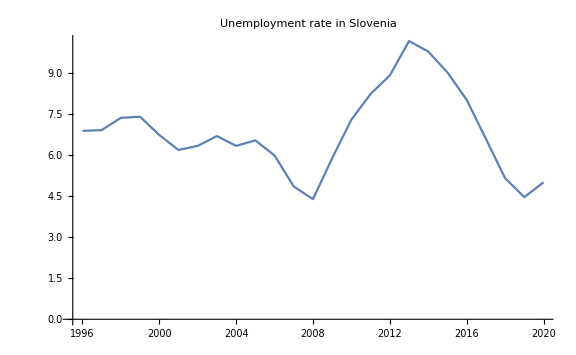

```mathematica
Narisi[Entity["Country","Slovenia"]]
```

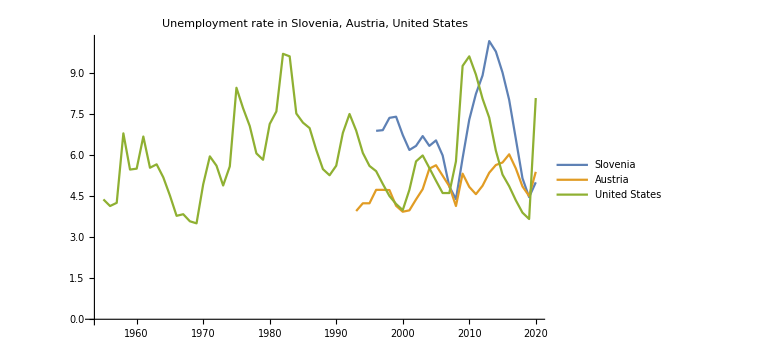

```mathematica
Narisi[Entity["Country","Slovenia"],Entity["Country","Austria"],Entity["Country","UnitedStates"]]
```

Primerjajmo slo

## Zemljevid brezposelnosti v državah OECD za posamezno leto

Kako izgleda zemljevid brezposelnosti za posamezno leto?

```mathematica
podatkiZaLeto[leto_]:=
```

```mathematica
GeoRegionValuePlot[CountryData["OECD"]->"GDPPerCapita",ImageSize->1200]
```

-Graphics-